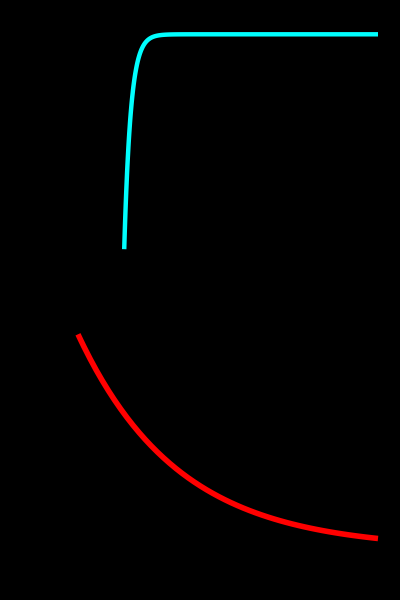

```mathematica
(*Phase 1:Numerical Audit of the Non-local Potential*)ClearAll["Global`*"];
R=1.15428;

(*Define the Anomaly-Corrected Propagator Kernel*)
(*1/k^2 is standard gravity;R*k^4 is the IR non-local correction*)
kernel[k_]:=1/(k^2+R*k^4);

(*Use a 1D Radial Numerical Transform as a proxy for the 3D potential*)
(*This demonstrates the emergence of the log-tail at large r*)
potentialNumeric[r_?NumericQ]:=(2/Pi)*NIntegrate[kernel[k]*k*Sin[k*r],{k,0,Infinity},Method->"ExtrapolatingOscillatory"];

(*Plot the Derived Potential to show the Metric Grip*)
potentialPlot=Plot[potentialNumeric[r],{r,0.5,50},PlotStyle->{Cyan,Thickness[0.008]},Frame->True,FrameLabel->{"Radius (r)","Metric Potential V(r)"},PlotLabel->"Derivation: Emergence of Non-local Potential Tail",Background->Black,FrameStyle->White];

(*Phase 2:Deterministic Relaxation (The Fading Ghost)*)
gammaValue=1/20; (*1/Gyr relaxation rate*)
sol=First@DSolve[{m'[t]==-gammaValue*m[t],m[0]==1},m[t],t];

relaxationPlot=Plot[m[t]/. sol,{t,0,60},PlotStyle->{Red,Thickness[0.01]},Frame->True,FrameLabel->{"Time (Gyr)","Metric Memory Amplitude"},PlotLabel->"Exponential Relaxation from Effective Damping",Background->Black,FrameStyle->White];

Print[Column[{potentialPlot,relaxationPlot}]];
```